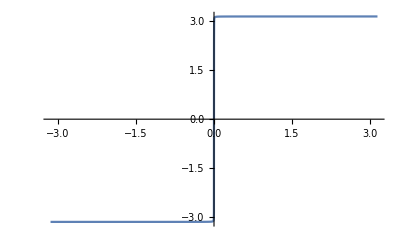

```mathematica
Plot[2 ArcTan[10000 Tan[x/2]],{x,-π,π}]
```

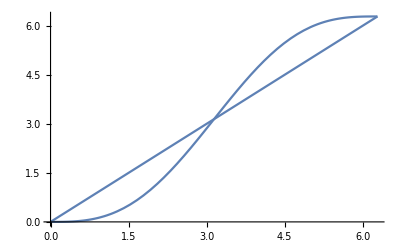

```mathematica
Show[Table[Plot[ea-e Sin[ea],{ea,0,2π}],{e,{0,1}}]]
```

```mathematica
Solve[√((1+e)/(1-e))Tan[ea/2]==Tan[ν/2],ea]
```

{{ea→ConditionalExpression[2 (ArcTan[Tan[ν/2]/(√((1+e)/(1-e)))]+π C[1]),C[1]∈Integers]}}

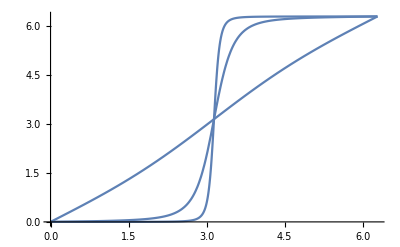

```mathematica
Show@Table[Plot[With[{ea=Mod[2ArcTan[Tan[ν/2]/(√((1+e)/(1-e)))],2π]},ea-e Sin[ea]],{ν,0,2π}],{e,{.1,.9,.99}}]
```

```mathematica
With[{n=1000},DiscretePlot[Binomial[n-m,m],{m,1,n},PlotRange->Full]]
```

-Graphics-

```mathematica
With[{n=100000000},SortBy[Table[{Binomial[n-m,m],m},{m,27639310,27639330}],First]//Last][[2]]
```

27639320

```mathematica
10000-2764
```

7236

```mathematica
2764*2
```

5528

```mathematica
1/√2//N
```

0.707107

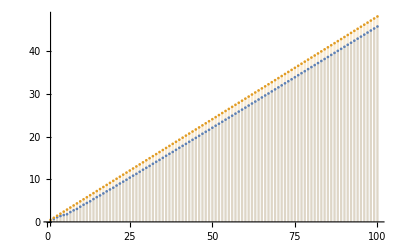

```mathematica
DiscretePlot[{Log@Max[Table[{Binomial[n-m,m],m},{m,1,n}]],Log[GoldenRatio^n]},{n,1,100}]
```

```mathematica
α=(5-√5)/10;
p=α/(1-α);
q=1-p;
```

```mathematica
N[α,10]
```

0.2763932023

```mathematica
Limit[(1/(p^(n p)q^(n q))1/(√(2π n p q)))^(1/(n+n p)),n->∞]//N
```

1.61803

```mathematica
N[2^(2/3),6]
```

1.5874

```mathematica
Limit[(1/((.5)^(n .5)(.5)^(n.5))1/(√(2π n .5 .5)))^(1/(n+n .5)),n->∞]//N
```

1.5874

```mathematica
Limit[(4^(n/2)/(√(π n)))^(1/(n+n/2)),n->∞]//N
```

1.5874

```mathematica
1-p
```

1+1/10 (-5+√5)

```mathematica
Solve[pp n==a (n +pp n),pp]
```

{{pp→-a/(-1+a)}}

```mathematica
-a/(-1+a)==a/(1-a)//Simplify
```

True

```mathematica
1.6180339887498951 4
```

6.47214